```mathematica
Кладов Валентин Алексеевич, 20361
```

```mathematica
1)
```

```mathematica
Clear f;
f:=Reverse[#,2]&;
f[{{1,2,3,4},
{a,b,c,d},
{5,6,7,8}}]
```

{{4,3,2,1},{d,c,b,a},{8,7,6,5}}

```mathematica
2)
```

```mathematica
Clear g;
g:=Thread[#1->#2]&;
g[{x,y,z},{1,2,3}]
```

{x→1,y→2,z→3}

```mathematica
3)
```

```mathematica
Clear h;
h:=Outer[D,#1,#2]&;
Det[h[{r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ]},{r,θ,ϕ}]]
```

r^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]+r^2 Cos[ϕ]^2 Sin[θ]^3+r^2 Cos[θ]^2 Sin[θ] Sin[ϕ]^2+r^2 Sin[θ]^3 Sin[ϕ]^2

```mathematica
Simplify[%]
```

r^2 Sin[θ]

```mathematica
4)
```

```mathematica
Clear[v,div,f,g,h];
div:=Inner[D,#1,#2,Plus]&;
div[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

h^(0,0,1)[x,y,z]+g^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]

```mathematica
0)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["titanic.csv"];
```

```mathematica
1)
```

```mathematica
data[[1]]
```

{PassengerId,Survived,Pclass,Name,Sex,Age,SibSp,Parch,Ticket,Fare,Cabin,Embarked}

```mathematica
2)
```

```mathematica
First[Dimensions[data]]-1
```

891

```mathematica
3)
```

```mathematica
survived = Delete[data[[All,2]],1];
pclass = Delete[data[[All,3]],1];
sex = Delete[data[[All,5]],1];
age = Delete[data[[All,6]],1];
```

```mathematica
4)
```

```mathematica
Count[sex,"female"]
```

314

```mathematica
Count[sex,"male"]
```

577

```mathematica
Count[Pick[sex,#==1&/@survived],"female"]/Count[Pick[sex,#==1&/@survived],"male"]
```

233/109

```mathematica
5)
```

```mathematica
N[Count[Pick[sex,#==1&/@survived],"female"]/Count[sex,"female"]]*100
```

74.2038

```mathematica
N[Count[Pick[sex,#==1&/@survived],"male"]/Count[sex,"male"]]*100
```

18.8908

```mathematica
{f[1],f[2],f[3]}=Table[N[Count[Pick[survived,#==i&/@pclass],1]/Count[pclass,i]]*100,{i,1,3}]
```

{62.963,47.2826,24.2363}

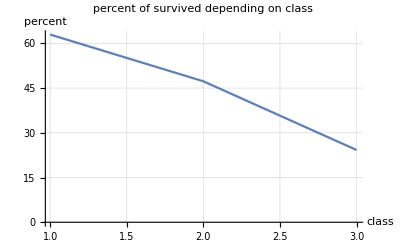

```mathematica
ListPlot[Table[{i,f[i]},{i,1,3}],PlotLabel->"percent of survived depending on class",AxesLabel->{"class","percent"},Joined->True,GridLines->Automatic]
```

```mathematica
6)
```

```mathematica
FullForm[data]
```

List[List["PassengerId","Survived","Pclass","Name","Sex","Age","SibSp","Parch","Ticket","Fare","Cabin","Embarked"],List[1,0,3,"Braund, Mr. Owen Harris","male",22,1,0,"A/5 21171",7.25,"","S"],888,List[890,1,1,"Behr, Mr. Karl Howell","male",26,0,0,111369,30,"C148","C"],List[891,0,3,"Dooley, Mr. Patrick","male",32,0,0,370376,7.75,"","Q"]]
 |  |  |  |

```mathematica
Count[age,""]
```

177

```mathematica
7)
```

```mathematica
nagel=Pick[age,#≠""&/@age];
Max[nagel]
Min[nagel]
Mean[nagel]
```

80

0.42

29.6991

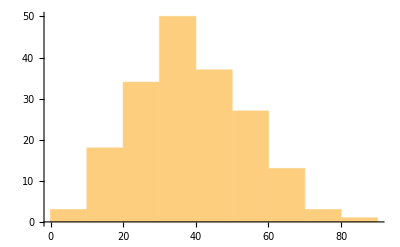
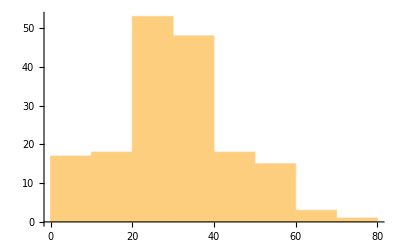
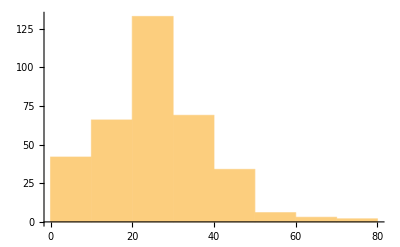

```mathematica
Table[Histogram[Pick[nagel,#==i&/@Pick[pclass,#≠""&/@age]],8],{i,1,3}]
```

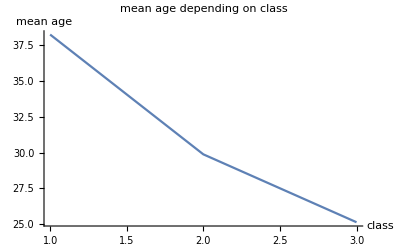

```mathematica
ListPlot[Table[{i,Mean[Pick[nagel,#==i&/@Pick[pclass,#≠""&/@age]]]},{i,1,3}], PlotLabel->"mean age depending on class",AxesLabel->{"class","mean age"},Joined->True]
```

```mathematica
8)
```

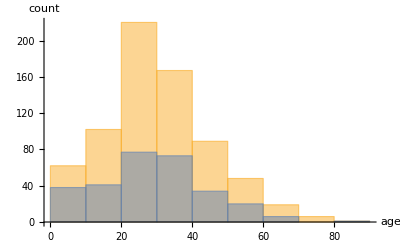

```mathematica
Histogram[{nagel,Pick[nagel,#==1&/@Pick[survived,#≠""&/@age]]},10,AxesLabel->{"age","count"}]
```